```mathematica
data = Import["C:\\Users\\Alexey\\Downloads\\Imitator.csv", "Table"];
```

```mathematica
data = data[[;;2401, 6;;15]];
```

```mathematica
Do[Subscript[V, i]=Array[Subscript[v, i],10],{i,1,2401}];
```

```mathematica
Do[Subscript[v, i][j]=data[[i,j]], {j,1,10}, {i, 1, 2401}]
```

```mathematica
traindata = data[[ ;;1600]];
validata = data[[1601;;2000]];
testdata = data[[2001;;]];
```

```mathematica
trainset=Table[Subscript[V, i-1]->Subscript[V, i][[1]],{i,2,1600}];
validset=Table[Subscript[V, i-1]->Subscript[V, i][[1]],{i,1602,2000}];
testset=Table[Subscript[V, i-1]->Subscript[V, i][[1]],{i, 2002,2401}];
```

```mathematica
Append[
```

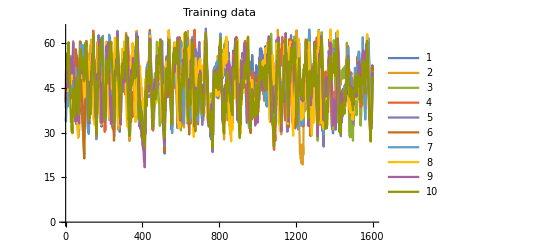
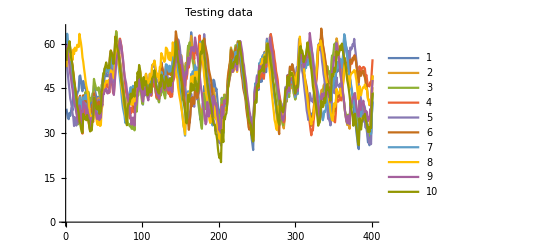
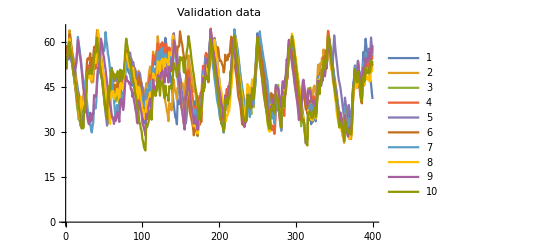

```mathematica
{ListLinePlot[Transpose[traindata],PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},PlotLabel->Style["Training data",15]],ListLinePlot[Transpose[testdata],PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},PlotLabel->Style["Testing data",15]],ListLinePlot[Transpose[validata],PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},PlotLabel->Style["Validation data",15]]}
```

```mathematica
pred=Predict[trainset,ValidationSet->validset,Method->"RandomForest",PerformanceGoal->"Quality"]
```

```mathematica
pred[Subscript[V, 1]]
```

39.8024

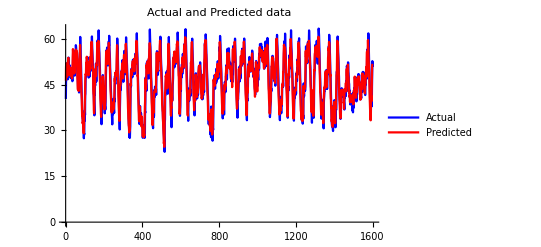

```mathematica
plotdata=traindata;
adata=Transpose[Take[traindata,All,1]]//Flatten;
pdata=Table[pred[Subscript[V, i]],{i,2,1600}];
ListLinePlot[{adata,pdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```

PredictorMeasurementsObject[…]

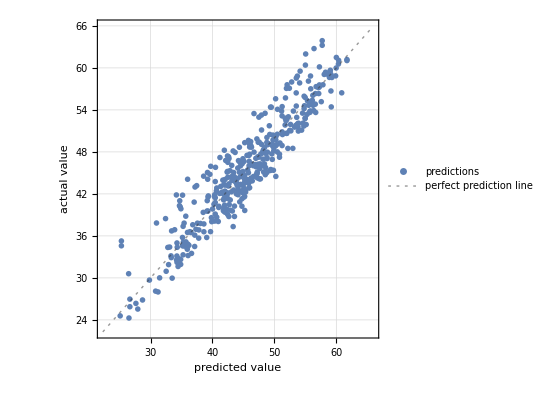

```mathematica
pm=PredictorMeasurements[pred,testset]
pm["ComparisonPlot"]
```

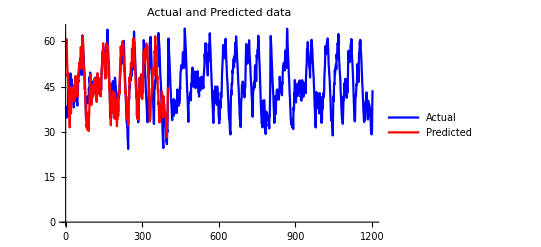

```mathematica
plottestdata=testdata;
atestdata=Transpose[Take[testdata,All,3]]//Flatten;
ptestdata=Table[pred[plottestdata[[i,3]]],{i,1,Length[testdata]}];
ListLinePlot[{atestdata,ptestdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```

```mathematica
plottestdata=testdata;
atestdata=Transpose[Take[testdata,All,1]]//Flatten;
ptestdata=Table[pred[plottestdata[[i]]],{i,1,Length[testdata]}];
ListLinePlot[{atestdata,ptestdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```

```mathematica
k=Table[pred[V,]
```